# Homework Fourier Interpolation

#### 1) Plot t = 0.03, 0.06, 0.08, 0.1

```mathematica
λ = 0.5;
k=10;
mymatrix = {};
```

```mathematica
For[i=0,i≤k,i++,
rows = {};
For[j=0,j≤k,j++,
Which[i==0 && j==0, AppendTo[rows,1],
i==k &&j==k, AppendTo[rows,1],
i==k && j==(k-1), AppendTo[rows,0],
i==(k-1) && j==k, AppendTo[rows,λ],
i==(k-1)&&j==(k-1), AppendTo[rows,1-(2*λ)],
i==0 && j==0, AppendTo[rows,1],
i==0 && j==1, AppendTo[rows,0],
i==j, AppendTo[rows, (1-(2*λ))],
i==(j+1), AppendTo[rows,λ],
i==(j-1), AppendTo[rows,λ],
i≠j,
AppendTo[rows,0]]];
AppendTo[mymatrix,rows]]
```

```mathematica
MatrixForm[mymatrix]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
initial = {};
For[i=0,i≤k,i++,
mo={};
For[j=0,j≤0,j++,
If[i==0&&j==0,
AppendTo[mo,20],
AppendTo[mo,0]]];
AppendTo[initial,mo]]
```

```mathematica
Subscript[t, 0]=initial
```

{{20},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
For[i=1,i≤10,i++,
Subscript[t, i]=mymatrix.Subscript[t, i-1]]
```

```mathematica
point= {};
For[i=1,i≤11,i++,
AppendTo[point,-6+i]]
```

```mathematica
For[i=0,i≤10,i++,
Subscript[d, i]= Transpose[Subscript[t, i]];
Subscript[d, i]=Subscript[d, i][[1]]]
```

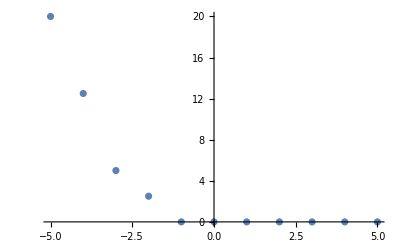

```mathematica
ListPlot[Thread[{point,Subscript[d, 3]}]]
```

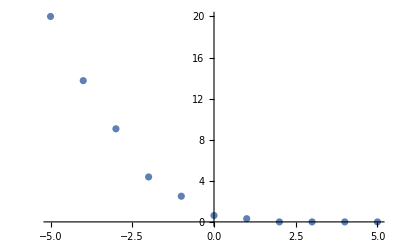

```mathematica
ListPlot[Thread[{point,Subscript[d, 6]}]]
```

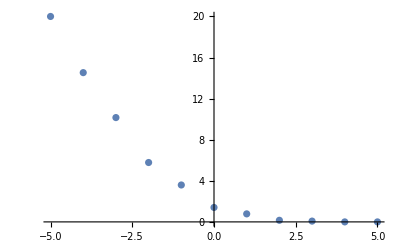

```mathematica
ListPlot[Thread[{point,Subscript[d, 8]}]]
```

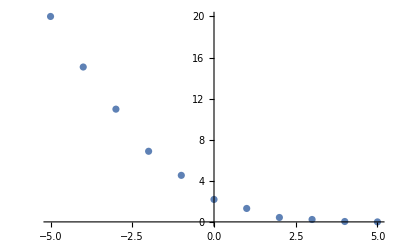

```mathematica
ListPlot[Thread[{point,Subscript[d, 10]}]]
```

```mathematica
2) When alpha equals 2
```

```mathematica
λ = 2;
k=10;
```

```mathematica
mymatrix = {};
For[i=0,i≤k,i++,
rows = {};
For[j=0,j≤k,j++,
Which[i==0 && j==0, AppendTo[rows,1],
i==k &&j==k, AppendTo[rows,1],
i==k && j==(k-1), AppendTo[rows,0],
i==(k-1) && j==k, AppendTo[rows,λ],
i==(k-1)&&j==(k-1), AppendTo[rows,1-(2*λ)],
i==0 && j==0, AppendTo[rows,1],
i==0 && j==1, AppendTo[rows,0],
i==j, AppendTo[rows, (1-(2*λ))],
i==(j+1), AppendTo[rows,λ],
i==(j-1), AppendTo[rows,λ],
i≠j,
AppendTo[rows,0]]];
AppendTo[mymatrix,rows]]
```

```mathematica
initial = {};
For[i=0,i≤k,i++,
mo={};
For[j=0,j≤0,j++,
If[i==0&&j==0,
AppendTo[mo,20],
AppendTo[mo,0]]];
AppendTo[initial,mo]]
```

```mathematica
MatrixForm[mymatrix]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -3 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | -3 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | -3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | -3 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | -3 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | -3 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | -3 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -3 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -3 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Subscript[t, 0]=initial
```

{{20},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
For[i=1,i≤10,i++,
Subscript[t, i]=mymatrix.Subscript[t, i-1]]
```

```mathematica
point= {};
For[i=1,i≤11,i++,
AppendTo[point,-6+i]]
```

```mathematica
For[i=0,i≤10,i++,
Subscript[d, i]= Transpose[Subscript[t, i]];
Subscript[d, i]=Subscript[d, i][[1]]]
```

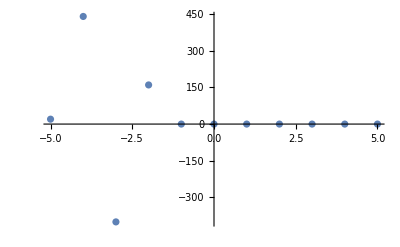

```mathematica
ListPlot[Thread[{point,Subscript[d, 3]}]]
```

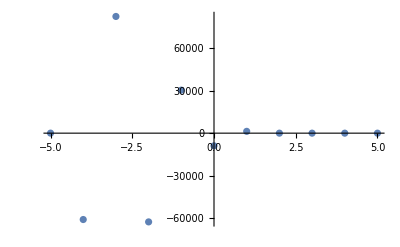

```mathematica
ListPlot[Thread[{point,Subscript[d, 6]}]]
```

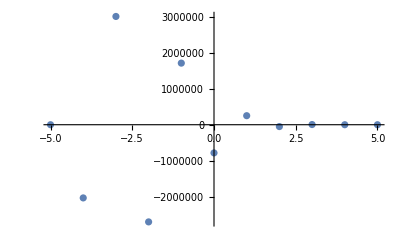

```mathematica
ListPlot[Thread[{point,Subscript[d, 8]}]]
```

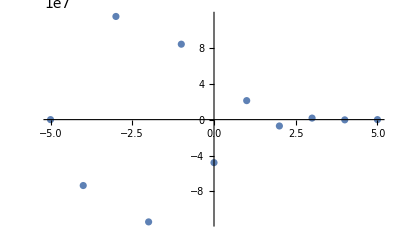

```mathematica
ListPlot[Thread[{point,Subscript[d, 10]}]]
```

```mathematica
(** Seems like the data is not behaving as well as it should have **)
```

```mathematica
3) Alpha equals 2 and delta(t) equals 0.001
```

```mathematica
λ = 0.2;
k=10;
mymatrix = {};
```

```mathematica
For[i=0,i≤k,i++,
rows = {};
For[j=0,j≤k,j++,
Which[i==0 && j==0, AppendTo[rows,1],
i==k &&j==k, AppendTo[rows,1],
i==k && j==(k-1), AppendTo[rows,0],
i==(k-1) && j==k, AppendTo[rows,λ],
i==(k-1)&&j==(k-1), AppendTo[rows,1-(2*λ)],
i==0 && j==0, AppendTo[rows,1],
i==0 && j==1, AppendTo[rows,0],
i==j, AppendTo[rows, (1-(2*λ))],
i==(j+1), AppendTo[rows,λ],
i==(j-1), AppendTo[rows,λ],
i≠j,
AppendTo[rows,0]]];
AppendTo[mymatrix,rows]]
```

```mathematica
MatrixForm[mymatrix]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.2 | 0.6 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2 | 0.6 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.2 | 0.6 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.2 | 0.6 | 0.2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.2 | 0.6 | 0.2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.2 | 0.6 | 0.2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.6 | 0.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.6 | 0.2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.6 | 0.2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
initial = {};
For[i=0,i≤k,i++,
mo={};
For[j=0,j≤0,j++,
If[i==0&&j==0,
AppendTo[mo,20],
AppendTo[mo,0]]];
AppendTo[initial,mo]]
```

```mathematica
Subscript[t, 0]=initial;
```

```mathematica
For[i=1,i≤10,i++,
Subscript[t, i]=mymatrix.Subscript[t, i-1]]
```

```mathematica
point= {};
For[i=1,i≤11,i++,
AppendTo[point,-6+i]]
```

```mathematica
For[i=0,i≤10,i++,
Subscript[d, i]= Transpose[Subscript[t, i]];
Subscript[d, i]=Subscript[d, i][[1]]]
```

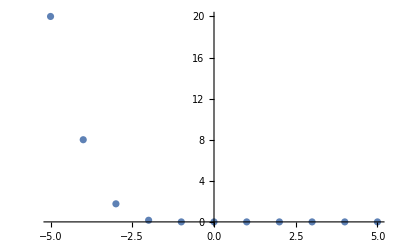

```mathematica
ListPlot[Thread[{point,Subscript[d, 3]}]]
```

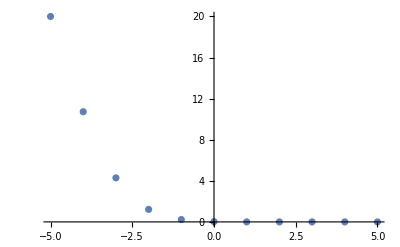

```mathematica
ListPlot[Thread[{point,Subscript[d, 6]}]]
```

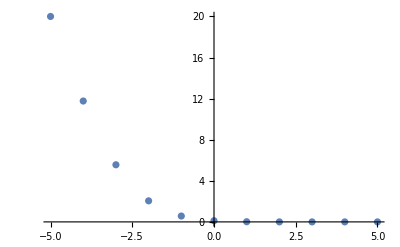

```mathematica
ListPlot[Thread[{point,Subscript[d, 8]}]]
```

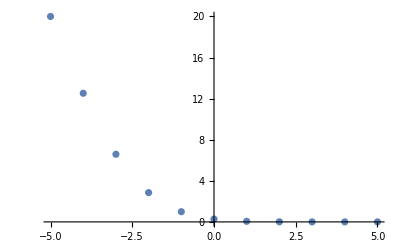

```mathematica
ListPlot[Thread[{point,Subscript[d, 10]}]]
```

```mathematica
(** Looks like that heat goes to 0 faster when lambda is smaller **)
```

### * ) Computing Fourier Coefficients

```mathematica
λ = 0.50;
k=10;
mymatrix = {};
For[i=0,i≤k,i++,
rows = {};
For[j=0,j≤k,j++,
Which[i==0 && j==0, AppendTo[rows,1],
i==k &&j==k, AppendTo[rows,1],
i==k && j==(k-1), AppendTo[rows,0],
i==(k-1) && j==k, AppendTo[rows,λ],
i==(k-1)&&j==(k-1), AppendTo[rows,1-(2*λ)],
i==0 && j==0, AppendTo[rows,1],
i==0 && j==1, AppendTo[rows,0],
i==j, AppendTo[rows, (1-(2*λ))],
i==(j+1), AppendTo[rows,λ],
i==(j-1), AppendTo[rows,λ],
i≠j,
AppendTo[rows,0]]];
AppendTo[mymatrix,rows]];
initial = {};
For[i=0,i≤k,i++,
mo={};
For[j=0,j≤0,j++,
If[i==0&&j==0,
AppendTo[mo,20],
AppendTo[mo,0]]];
AppendTo[initial,mo]];
Subscript[t, 0]=initial;
For[i=1,i≤10,i++,
Subscript[t, i]=mymatrix.Subscript[t, i-1]];
```

```mathematica
(** This is for lambda = 0.5 **)
```

```mathematica
M = 11;
dftm = {};
For[k =0, k ≤ M -1, ++k, 
row = {};
For[i =0, i ≤ M-1, ++i,
xi = 2*Pi/M * i;
AppendTo[row, E^(I*k*xi)];

];

AppendTo[dftm,row];
];
(** Source: Fourier.nb **)
```

```mathematica
dftm = Simplify[dftm];
MatrixForm[dftm]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | (-1)^(2/11) | (-1)^(4/11) | (-1)^(6/11) | (-1)^(8/11) | (-1)^(10/11) | -(-1)^(1/11) | -(-1)^(3/11) | -(-1)^(5/11) | -(-1)^(7/11) | -(-1)^(9/11)
1 | (-1)^(4/11) | (-1)^(8/11) | -(-1)^(1/11) | -(-1)^(5/11) | -(-1)^(9/11) | (-1)^(2/11) | (-1)^(6/11) | (-1)^(10/11) | -(-1)^(3/11) | -(-1)^(7/11)
1 | (-1)^(6/11) | -(-1)^(1/11) | -(-1)^(7/11) | (-1)^(2/11) | (-1)^(8/11) | -(-1)^(3/11) | -(-1)^(9/11) | (-1)^(4/11) | (-1)^(10/11) | -(-1)^(5/11)
1 | (-1)^(8/11) | -(-1)^(5/11) | (-1)^(2/11) | (-1)^(10/11) | -(-1)^(7/11) | (-1)^(4/11) | -(-1)^(1/11) | -(-1)^(9/11) | (-1)^(6/11) | -(-1)^(3/11)
1 | (-1)^(10/11) | -(-1)^(9/11) | (-1)^(8/11) | -(-1)^(7/11) | (-1)^(6/11) | -(-1)^(5/11) | (-1)^(4/11) | -(-1)^(3/11) | (-1)^(2/11) | -(-1)^(1/11)
1 | -(-1)^(1/11) | (-1)^(2/11) | -(-1)^(3/11) | (-1)^(4/11) | -(-1)^(5/11) | (-1)^(6/11) | -(-1)^(7/11) | (-1)^(8/11) | -(-1)^(9/11) | (-1)^(10/11)
1 | -(-1)^(3/11) | (-1)^(6/11) | -(-1)^(9/11) | -(-1)^(1/11) | (-1)^(4/11) | -(-1)^(7/11) | (-1)^(10/11) | (-1)^(2/11) | -(-1)^(5/11) | (-1)^(8/11)
1 | -(-1)^(5/11) | (-1)^(10/11) | (-1)^(4/11) | -(-1)^(9/11) | -(-1)^(3/11) | (-1)^(8/11) | (-1)^(2/11) | -(-1)^(7/11) | -(-1)^(1/11) | (-1)^(6/11)
1 | -(-1)^(7/11) | -(-1)^(3/11) | (-1)^(10/11) | (-1)^(6/11) | (-1)^(2/11) | -(-1)^(9/11) | -(-1)^(5/11) | -(-1)^(1/11) | (-1)^(8/11) | (-1)^(4/11)
1 | -(-1)^(9/11) | -(-1)^(7/11) | -(-1)^(5/11) | -(-1)^(3/11) | -(-1)^(1/11) | (-1)^(10/11) | (-1)^(8/11) | (-1)^(6/11) | (-1)^(4/11) | (-1)^(2/11))

```mathematica
dftm = dftm/Sqrt[M];
```

```mathematica
For[i=0,i≤10,i++,
Subscript[x, i]=N[Simplify[dftm.Subscript[t, i]]];
]
```

```mathematica
M =11;
Clear[x];
For[i=0,i≤10,i++,
Subscript[interp, i]={};
For[k =0, k ≤ M -1, ++k, 

Subscript[f, i] = 1/Sqrt[M]*(
Re[Subscript[x, i][[k+1]]]*Cos[k* 2*Pi/M * x] +
Im[Subscript[x, i][[k+1]]]*Sin[k* 2*Pi/M * x]
);
AppendTo[Subscript[interp, i], Subscript[f, i]];

];]
```

```mathematica
(** This for loop will give me my fourier coefficient matrix for each time interval **)
```

```mathematica
(** Example **)
Subscript[interp, 5]
```

{{4.31818},{(9.84192 Cos[(2 π x)/11]+5.94197 Sin[(2 π x)/11])/(√11)},{(5.1108 Cos[(4 π x)/11]+4.63357 Sin[(4 π x)/11])/(√11)},{(4.01212 Cos[(6 π x)/11]+2.61276 Sin[(6 π x)/11])/(√11)},{(3.81986 Cos[(8 π x)/11]+1.54279 Sin[(8 π x)/11])/(√11)},{(3.22065 Cos[(10 π x)/11]+0.786046 Sin[(10 π x)/11])/(√11)},{(3.22065 Cos[(12 π x)/11]-0.786046 Sin[(12 π x)/11])/(√11)},{(3.81986 Cos[(14 π x)/11]-1.54279 Sin[(14 π x)/11])/(√11)},{(4.01212 Cos[(16 π x)/11]-2.61276 Sin[(16 π x)/11])/(√11)},{(5.1108 Cos[(18 π x)/11]-4.63357 Sin[(18 π x)/11])/(√11)},{(9.84192 Cos[(20 π x)/11]-5.94197 Sin[(20 π x)/11])/(√11)}}

```mathematica
(** This is my 6th fourier coefficient matrix for the 6th time interval **)
```

```mathematica
newmatrix={};
For[i=0,i≤10,i++,
AppendTo[newmatrix,Subscript[interp, i][[8]]]]
```

```mathematica
(**I decided to take the 9th entry of my all my fourier coefficient matrix**)
```

```mathematica
matrix = {};
x=-5;
For[i=-5,i≤5,i++,
AppendTo[matrix,{i,Transpose[newmatrix][[1]][[i+6]]}];
x=x+1;]
```

```mathematica
matrix
```

{{-5,0.7553},{-4,-1.36688},{-3,0.846111},{-2,0.355495},{-1,-0.949656},{0,1.15173},{1,-0.388295},{2,-0.590306},{3,1.07942},{4,-0.91819},{5,0.0507596}}

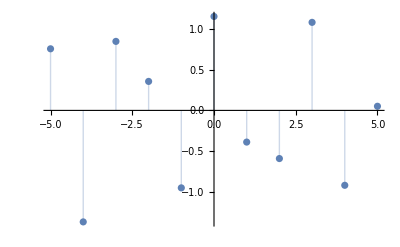

```mathematica
ListPlot[matrix, Filling->Axis]
```

```mathematica
(** Since code is just going to repeat, I will just show the graphs of each lambda values **)
```

### Lambda = 0.35

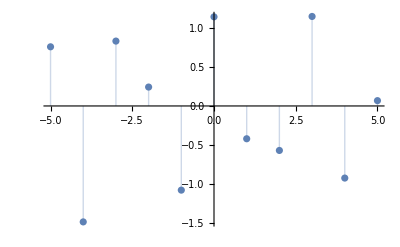

-Graphics-

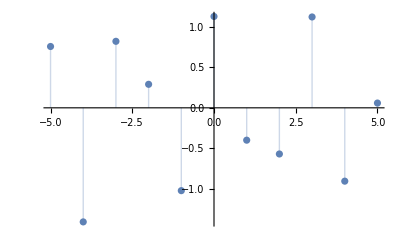
### Lambda = 0.45 -Graphics-

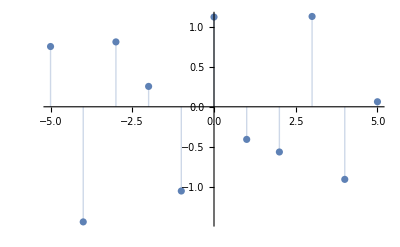
#### Lambda = 0.4 -Graphics-

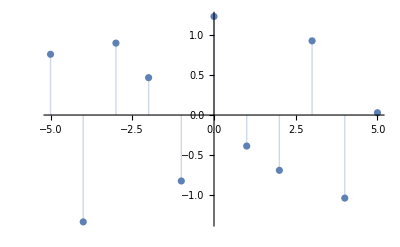
#### Lambda = 0.55 -Graphics-

```mathematica
(** It seems that different lambda values have little to no effect on the graph **)
```

Implicit FDM

```mathematica
matrix = {};
k=10;
λ=0.5;
For[i=0,i≤k,i++,
rows={};
For[j=0,j≤k,j++,
Which[
i==0&&j==0,AppendTo[rows,1],
i==k &&j==k, AppendTo[rows,1],
i==k&&j==(k-1),AppendTo[rows,0],
i==0 && j==1, AppendTo[rows,0],
i==j, AppendTo[rows,(1+(2*λ))],
i==j+1, AppendTo[rows,-λ ],
i==j-1, AppendTo[rows,-λ ] ,
i≠j, AppendTo[rows,0]]];
AppendTo[matrix,rows]]
```

```mathematica
MatrixForm[matrix]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.5 | 2. | -0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.5 | 2. | -0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.5 | 2. | -0.5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.5 | 2. | -0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.5 | 2. | -0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.5 | 2. | -0.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.5 | 2. | -0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.5 | 2. | -0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.5 | 2. | -0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
initial = {};
For[i=0,i≤k,i++,
row = {};
For[j=0,j≤0,j++,
If[i==0 && j==0,
AppendTo[row,20],
AppendTo[row,0]]];
AppendTo[initial,row]];
MatrixForm[initial]
```

(20
0
0
0
0
0
0
0
0
0
0)

```mathematica
Subscript[t, 0]=initial;
For[i=1,i≤k,i++,
Subscript[t, i]=LinearSolve[matrix,Subscript[t, i-1]]]
```

```mathematica
points= {};
For[i=1,i≤11,i++,
AppendTo[points,-6+i]];
```

```mathematica
For[i=0,i≤10,i++,
Subscript[m, i]= Transpose[Subscript[t, i]];
Subscript[m, i]=Subscript[m, i][[1]]]
```

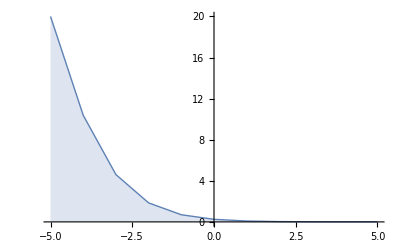

```mathematica
ListLinePlot[Thread[{point,Subscript[m, 3]}],Filling->Axis, PlotStyle->Thick]
```

```mathematica
ListPlot3D[Thread[{point,Subscript[m, 6]}]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Thread[{point,Subscript[m, 8]}], FormatType->TraditionalForm, PlotStyle->Dashed]
```

-Graphics3D-

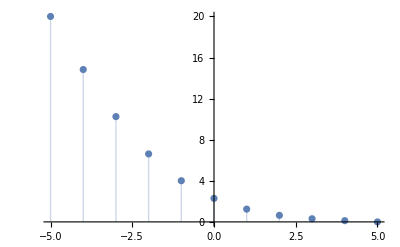

```mathematica
ListPlot[Thread[{point,Subscript[m, 10]}],Filling->Axis]
```

```mathematica
(** The different graphing style was just for fun **)
```

Crank Nicolson FDM

```mathematica
Clear[λ];
k=10;
mymatrix={};
For[i=0,i≤k,i++,
rows = {};
For[j=0,j≤k,j++,
Which[i==0 && j==0, AppendTo[rows,1],
i==k &&j==k, AppendTo[rows,1],
i==k && j==(k-1), AppendTo[rows,0],
i==(k-1) && j==k, AppendTo[rows,λ],
i==(k-1)&&j==(k-1), AppendTo[rows,(2*(1-λ))],
i==0 && j==0, AppendTo[rows,1],
i==0 && j==1, AppendTo[rows,0],
i==j, AppendTo[rows, (2*(1-λ))],
i==(j+1), AppendTo[rows,λ],
i==(j-1), AppendTo[rows,λ],
i≠j,
AppendTo[rows,0]]];
AppendTo[mymatrix,rows]]
```

```mathematica
MatrixForm[mymatrix]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | 2 (1-λ) | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | λ | 2 (1-λ) | λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ | 2 (1-λ) | λ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 2 (1-λ) | λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | λ | 2 (1-λ) | λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | λ | 2 (1-λ) | λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ | 2 (1-λ) | λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 2 (1-λ) | λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ | 2 (1-λ) | λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
matrix = {};
k=10;
Clear[λ];
For[i=0,i≤k,i++,
rows={};
For[j=0,j≤k,j++,
Which[
i==0&&j==0,AppendTo[rows,1],
i==k &&j==k, AppendTo[rows,1],
i==k&&j==(k-1),AppendTo[rows,0],
i==0 && j==1, AppendTo[rows,0],
i==j, AppendTo[rows,(2*(1+λ))],
i==j+1, AppendTo[rows,-λ ],
i==j-1, AppendTo[rows,-λ ] ,
i≠j, AppendTo[rows,0]]];
AppendTo[matrix,rows]]
```

```mathematica
MatrixForm[matrix]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-λ | 2 (1+λ) | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -λ | 2 (1+λ) | -λ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -λ | 2 (1+λ) | -λ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -λ | 2 (1+λ) | -λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -λ | 2 (1+λ) | -λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -λ | 2 (1+λ) | -λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -λ | 2 (1+λ) | -λ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 2 (1+λ) | -λ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -λ | 2 (1+λ) | -λ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
initial = {};
For[i=0,i≤10,i++,
rows={};
For[j=0,j≤0,j++,
If[i==0 &&j==0, 
AppendTo[rows,20],
AppendTo[rows,0]]];
AppendTo[initial,rows]]
```

```mathematica
Subscript[s, 0]=initial;
λ = 0.5;
```

```mathematica
For[i=1,i≤21,i++,
If[EvenQ[i]==True,
Subscript[s, i]=LinearSolve[matrix,Subscript[s, i-1]],
Subscript[s, i]=mymatrix.Subscript[s, i-1]]]
```

```mathematica
points= {};
For[i=1,i≤11,i++,
AppendTo[points,-6+i]];
```

```mathematica
For[i=0,i≤10,i++,
Subscript[m, i]= Transpose[Subscript[s, 2*i]];
Subscript[m, i]=Subscript[m, i][[1]]]
```

```mathematica
(** I multiplied the index of s by 2 because I'm not interested in the half time step **)
```

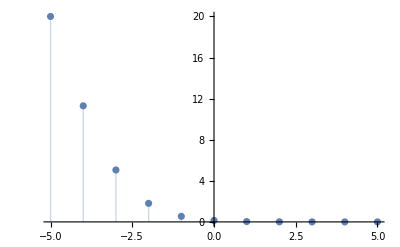

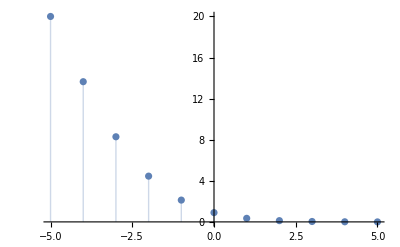

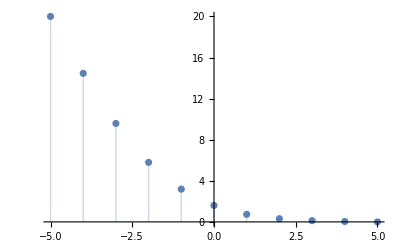

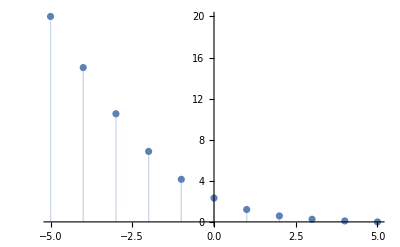

```mathematica
ListPlot[Thread[{point,Subscript[m, 3]}],Filling->Axis, PlotStyle->Thick]
ListPlot[Thread[{point,Subscript[m, 6]}],Filling->Axis, PlotStyle->Thick]
ListPlot[Thread[{point,Subscript[m, 8]}],Filling->Axis, PlotStyle->Thick]
ListPlot[Thread[{point,Subscript[m, 10]}],Filling->Axis, PlotStyle->Thick]
```